```mathematica
ZTransform[v[k+2],k,z]
```

-z^2 v[0]-z v[1]+z^2 ZTransform[v[k],k,z]

```mathematica
v[-5]+v[-4]/z+v[-3]/z^2+v[-2]/z^3+v[-1]/z^4+ZTransform[v[k],k,z]/z^5
```

```mathematica
Factor[(2+2 √2)/(4(z-(√2)/2))+(2-2 √2)/(4(z+(√2)/2))]
```

-(4 (1+z))/((√2-2 z) (√2+2 z))

```mathematica
Apart[(2z)/(-1+2 z^2)]
```

(2 z)/(-1+2 z^2)

```mathematica
ZTransform[-2^(-1-k/2) (-1+(-1)^(1+k)-√2+(-1)^k √2),k,z]
```

```mathematica
(2 z (1+z))/(-1+2 z^2)
Apart[%]
```

(2 z (1+z))/(-1+2 z^2)

1+(1+2 z)/(-1+2 z^2)

```mathematica
InverseZTransform[((1+√2)*z)/(2z-√2)+((1-√2)*z)/(2z+√2),z,k]
```

2^(-3/2-k/2) (2-2 (-1)^k+√2+(-1)^k √2)

```mathematica
RSolve[{2v[k+2]-v[k]==0,v[0]==1,v[1]==1},v[k],k]
```

{{v[k]→-2^(-1-k/2) (-1+(-1)^(1+k)-√2+(-1)^k √2)}}

-2^(-1-k/2) (-1+(-1)^(1+k)-√2+(-1)^k √2)

Rango de Convergencia&&(2 z (1+z))/(-1+2 z^2)

{{-2.,2.-3.46382×10^-16 ⅈ},{-1.,2.+0. ⅈ},{0.,1.+0. ⅈ},{1.,1.+8.65956×10^-17 ⅈ},{2.,0.5+8.65956×10^-17 ⅈ},{3.,0.5+8.65956×10^-17 ⅈ}}

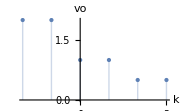

(-2)^(1+k)+2^(1+k)

Rango de Convergencia&&(8 z)/(-4+z^2)

```mathematica
v1= -2^(-1-k/2) (-1+(-1)^(1+k)-√2+(-1)^k √2)
"Rango de Convergencia"  && ZTransform[v1,k,z]  
list1=Table[{k,v1},{k,-2,3,1.}];
list1
ListPlot[list1,AxesLabel->{"k","vo"},Filling->Axis,ImageSize->Small,PlotStyle->PointSize[Medium],PlotRange->All]
```